```mathematica
points = Import["C:\\Users\\mouze\\Desktop\\practice\\project\\project\\in.txt", "Table"][[2;;]];
polygon =Import["C:\\Users\\mouze\\Desktop\\practice\\project\\project\\out.txt", "Table"][[2;;]]
```

{{-1.87938,-0.101262},{-0.783653,0.95143},{1.02205,0.869363},{1.8307,0.288838},{1.91843,0.102253},{1.65012,-0.994884},{-1.72664,-0.925785},{-1.87938,-0.101262}}

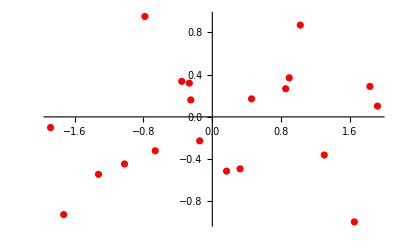

```mathematica
ListPlot[points,PlotStyle->Red, PlotRange->All]
```

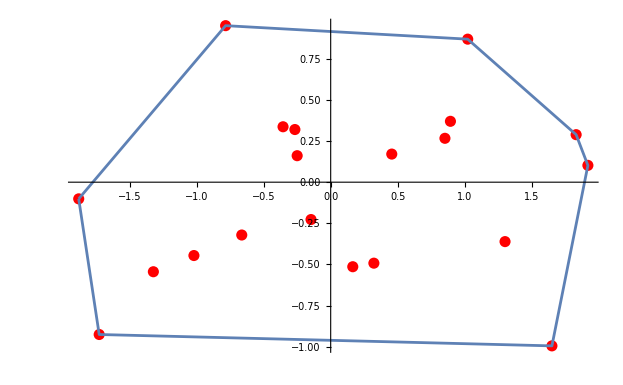

```mathematica
Show[ListPlot[points,PlotStyle->Red], ListLinePlot[polygon], PlotRange->All]
```